```mathematica
makeplot[n_]:=Plot[(1/(y^y (1-y)^(1-y)))^n,{y,0,0.45},AxesLabel->{"",""},Ticks-> {Table[x,{x,0,0.45,0.05}],Automatic}, PlotRange->All]
```

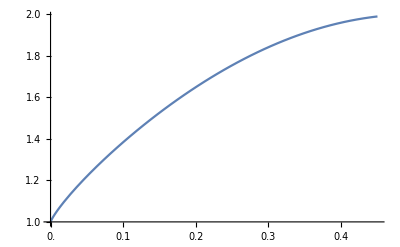

```mathematica
makeplot[1]
```

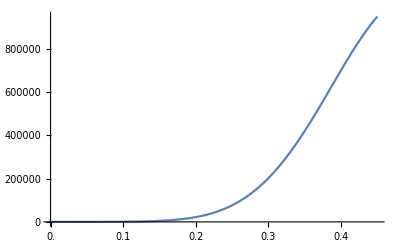

```mathematica
makeplot[20]
```

```mathematica
makeplot[100]
```

-Graphics-

```mathematica
makeplot[1000]
```

-Graphics-

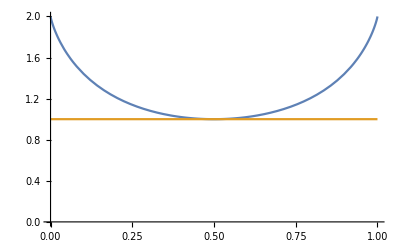

```mathematica
Plot[{2p^p(1-p)^(1-p),1},{p,0,1},AxesLabel->{"",""},PlotRange-> {0,2}]
```

```mathematica
h[x_]:=1/(x^x(1-x)^(1-x))
n1=200
Show[
Plot[{E h[x/(n1+1)]^(n1+1)},{x,0,n1*0.4}],
DiscretePlot[Binomial[n1,k],{k,0,n1*0.4}]
]
```

200

-Graphics-

2000

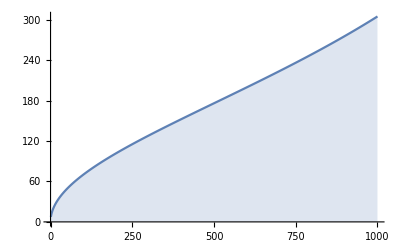

```mathematica
n1=2000
DiscretePlot[E h[k/(n1+1)]^(n1+1)/Binomial[n1,k],{k,0,n1/2}]
```

10

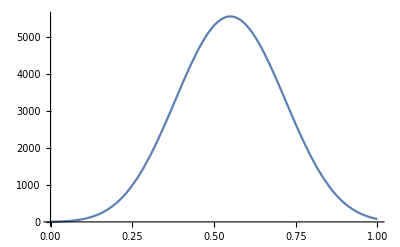

```mathematica
n=10
Plot[{Exp[(n+1)Log@(n+1)-(n-x n+1)Log@(n-x n+1)-x n Log@ (x n)+1],E/□},{x,0,1}]
n=.
```

```mathematica
Exp[(n+1)Log@(n+1)-(n-x n+1)Log@(n-x n+1)-x n Log@ (x n)+1]//FullSimplify
```

ⅇ (1+n)^(1+n) (n x)^(-n x) (1+n-n x)^(-1+n (-1+x))